```mathematica
nn=501;
ll=IntegerPart[nn/10];
prec=128;
nData=2000;
γ=1/2//N[#,prec]&;
λ=4/7//N[#,prec]&;
a0=λ//N[#,prec]&;
a1=(1-γ)/2//N[#,prec]&;
a2=(1+γ)/2//N[#,prec]&;
```

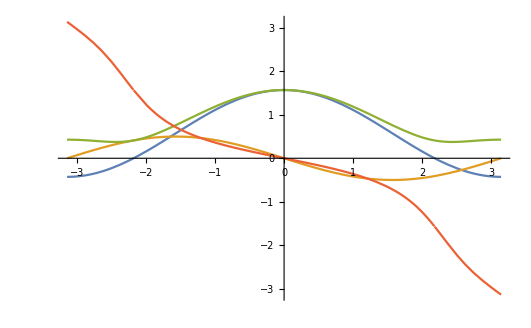

```mathematica
α[θ_]=(a0+(a2+a1) Cos[θ]);
β[θ_]=(a1-a2) Sin[θ];
ω[θ_]=Sqrt[α[θ]^2+β[θ]^2];
ϕ[θ_]=ArcTan[α[θ],β[θ]];
Plot[{α[x],β[x],ω[x],ϕ[x]},{x,-π,π}]
```

```mathematica
t=Table[k,{k,-(nn-1)/2,(nn-1)/2}];
(*mCos=Table[RandomInteger[{0,1}]-1/2,{k,1,(nn-1)/2}];
mCos0=RandomInteger[{0,1}]-1/2;
mSin=Table[RandomInteger[{0,1}]-1/2,{k,1,(nn-1)/2}];
mSin0=RandomInteger[{0,1}]-1/2;*)
```

```mathematica
(*MPlusBand=((If[#==0,(mCos0+mSin0)/2,(mCos⟦Abs[#]⟧+mSin⟦Abs[#]⟧)/2]) E^(I Sign[(2 π)/nn #] ϕ[Abs[(2 π)/nn #]])&/@t)//RotateLeft[#,(nn-1)/2]&//Fourier//Chop;
MMinusAntiBand=((If[#==0,(mCos0-mSin0)/2,(mCos⟦Abs[#]⟧-mSin⟦Abs[#]⟧)/2]) E^(I Sign[(2 π)/nn #] ϕ[Abs[(2 π)/nn #]])&/@t)//RotateLeft[#,(nn-1)/2]&//Fourier//Chop;*)
```

```mathematica
(*MPlus=Table[RotateRight[Take[MPlusBand,ll],j-1],{j,ll}];
MMinus=Table[RotateLeft[Take[MMinusAntiBand,ll],j-1],{j,ll}];*)
```

```mathematica
Now
μ=2//N[#,prec]&;
βT=RandomReal[{1/1000,1/1100}]//N[#,prec]&;
p[l_]=1/(Exp[βT (ω[((2 π)/nn) l]-μ)]+1);
Data=Table[
mCos=Table[If[RandomReal[]>p[k],-(1/2),1/2],{k,1,(nn-1)/2}];
mCos0=If[RandomReal[]>p[0],-(1/2),1/2];
mSin=Table[If[RandomReal[]>p[k],-(1/2),1/2],{k,1,(nn-1)/2}];
mSin0=If[RandomReal[]>p[0],-(1/2),1/2];
MPlusBand=((If[#==0,(mCos0+mSin0)/2,(mCos⟦Abs[#]⟧+mSin⟦Abs[#]⟧)/2]) E^(I Sign[(2 π)/nn #] ϕ[Abs[(2 π)/nn #]])&/@t)//RotateLeft[#,(nn-1)/2]&//Fourier;
MMinusAntiBand=((If[#==0,(mCos0-mSin0)/2,(mCos⟦Abs[#]⟧-mSin⟦Abs[#]⟧)/2]) E^(I Sign[(2 π)/nn #] ϕ[Abs[(2 π)/nn #]])&/@t)//RotateLeft[#,(nn-1)/2]&//Fourier;
(*MEspRed=
Table[RotateRight[Take[MPlusBand,ll],j-1],{j,ll}]
+Table[RotateLeft[Take[MMinusAntiBand,ll],j-1],{j,ll}];
Flatten[MEspRed]-Mean[Flatten[MEspRed]],*)
Join[Take[MPlusBand,ll],Take[MMinusAntiBand,ll]],
{ii,nData}];
Print["Aquí"];
DataCentered=Data-(Mean/@Data);
Now
```

Wed 9 May 2018 16:08:10GMT-5.

Aquí

Wed 9 May 2018 16:16:42GMT-5.

```mathematica
Cov=Sum[TensorProduct[DataCentered[[i]],DataCentered[[i]]],{i,nData}]//Timing;
Cov[[1]]
```

27.7997

```mathematica
EigenCov=Eigensystem[Cov[[2]]]//Timing;
EigenCov[[1]]
```

5.28456

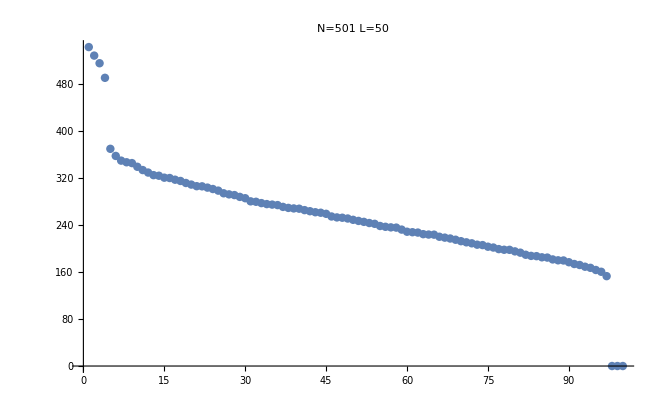

```mathematica
ListPlot[EigenCov[[2,1]]//Take[#,;;]&,PlotRange->All,PlotLabel-> "N=501  L=50"]
```

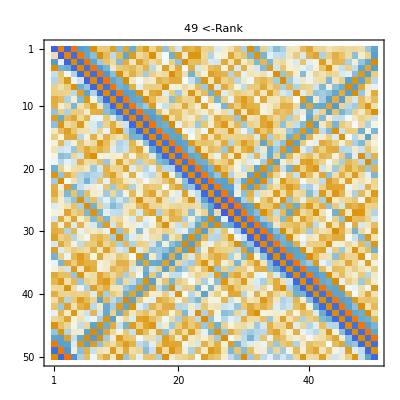
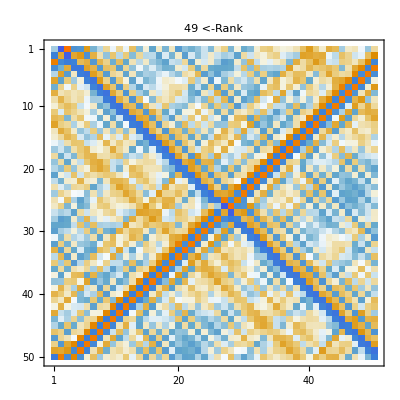
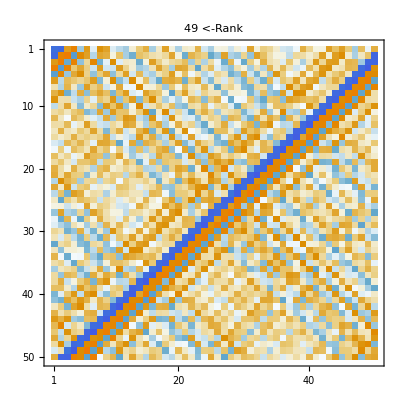
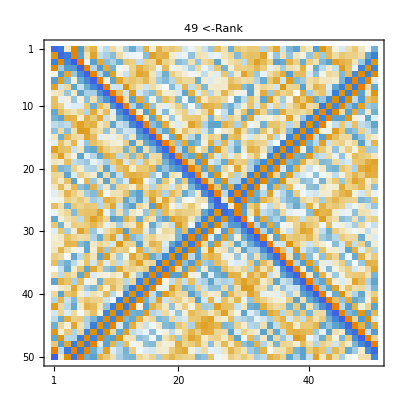
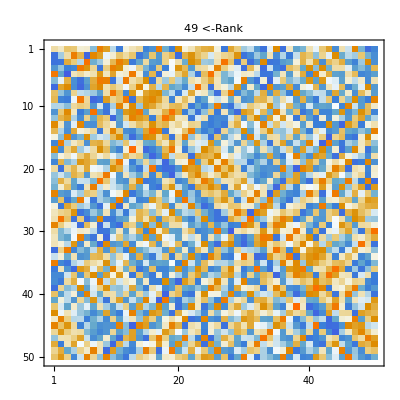

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»

```mathematica
nPCA=5;
BAB=Table[Partition[EigenCov⟦2,2,i⟧,ll],{i,nPCA}];
M=Table[Table[RotateRight[BAB⟦i,1⟧,j-1],{j,1,ll}]+Table[RotateLeft[BAB⟦i,2⟧,j-1],{j,1,ll}],{i,nPCA}];
Plots3D=Table[ListPlot3D[M⟦i⟧,PlotRange->All,PlotLabel->"<-Rank"MatrixRank[M⟦i⟧]],{i,nPCA}];
PlotsMatrices=Table[MatrixPlot[M⟦i⟧,PlotRange->All,PlotLabel->"<-Rank"MatrixRank[M⟦i⟧]],{i,nPCA}]
Plots3D⟦1⟧
Plots3D⟦2⟧
Plots3D⟦3⟧
Plots3D⟦4⟧
Plots3D⟦5⟧
```

```mathematica
.10
```

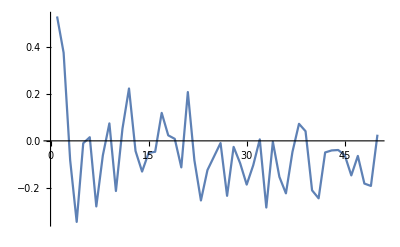

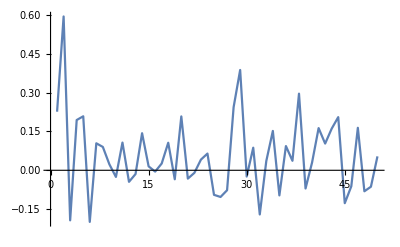

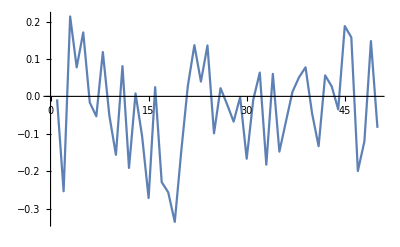

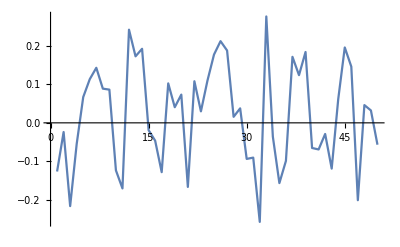

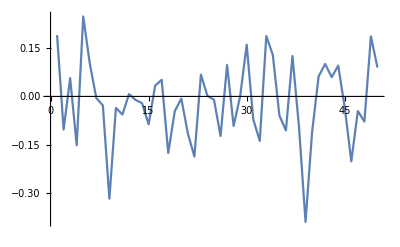

```mathematica
M⟦1⟧⟦1,All⟧//ListLinePlot[#,PlotRange->All]&
M⟦2⟧⟦1,All⟧//ListLinePlot[#,PlotRange->All]&
M⟦3⟧⟦1,All⟧//ListLinePlot[#,PlotRange->All]&
M⟦4⟧⟦1,All⟧//ListLinePlot[#,PlotRange->All]&
M⟦5⟧⟦1,All⟧//ListLinePlot[#,PlotRange->All]&
```

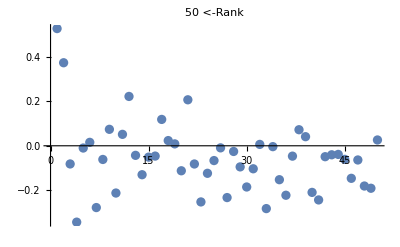

```mathematica
Table[ListPlot[M⟦i,1⟧,PlotLabel->"<-Rank"MatrixRank[M⟦i⟧]],{i,1,1}]
```

```mathematica
Table[ListPlot[Diagonal[M⟦i⟧],PlotLabel->"<-Rank"MatrixRank[M⟦i⟧]],{i,1,nPCA}];
```

```mathematica
Length[Partition[Mean[Data],ll]]
```

2

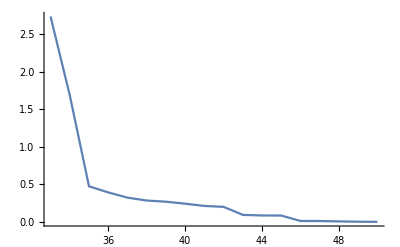

```mathematica
MMeanBAB=Partition[Mean[Data],ll];
MMean=Table[RotateRight[MMeanBAB⟦1⟧,j-1],{j,1,ll}]+Table[RotateLeft[MMeanBAB⟦2⟧,j-1],{j,1,ll}];
Table[MatrixPlot[M⟦i⟧,PlotLabel->"<-Rank"MatrixRank[M⟦i⟧]],{i,nPCA}];
s[x_]=-(1/2-x) Log[2,1/2-x]-(1/2+x) Log[2,1/2+x];
SVD=SingularValueDecomposition[M⟦1⟧+MMean];
(EntSpecRest=(s/@(SVD⟦2⟧//Diagonal))//-Log[#]&)//ListLinePlot[#,PlotRange->All]&
SVD⟦2⟧//Diagonal//N[#,4]&;
```

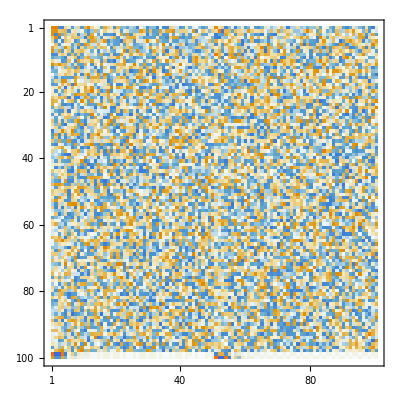

```mathematica
MatrixPlot[EigenCov[[2,2]]]
```

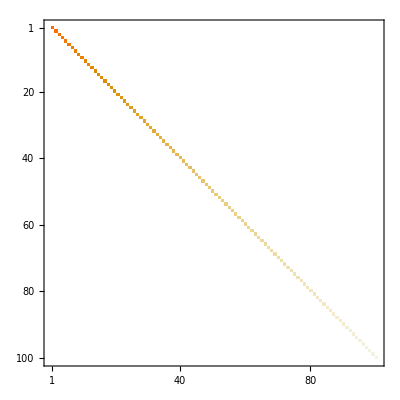

```mathematica
EigenCov[[2,1]]//DiagonalMatrix//MatrixPlot
```

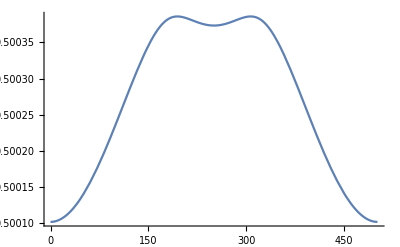

```mathematica
Plot[p[l],{l,0,nn}]
```